```mathematica
$Assumptions = {ϕ ∈ Reals, d ∈ Reals}
```

{ϕ∈ℝ,d∈ℝ}

```mathematica
ω = Exp[I 2 π/3]
```

ⅇ^((2 ⅈ π)/3)

```mathematica
Δ = d Exp[I ϕ]
```

d ⅇ^(ⅈ ϕ)

```mathematica
d=1
```

1

```mathematica
ϵ0 = FullSimplify[2 Re[Δ]]
```

2 d Cos[ϕ]

```mathematica
ϵ1 = FullSimplify[ComplexExpand[2 Re[ω Δ]]]
```

-2 d Sin[π/6+ϕ]

```mathematica
ϵ2 = FullSimplify[ComplexExpand[2 Re[ω^2 Δ]]]
```

-2 d Sin[π/6-ϕ]

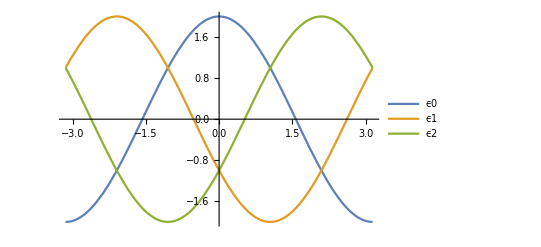

```mathematica
Plot[{ϵ0, ϵ1, ϵ2}, {ϕ, -π, π}, PlotLegends->{"ϵ0", "ϵ1", "ϵ2"}]
```